### Check quadrants

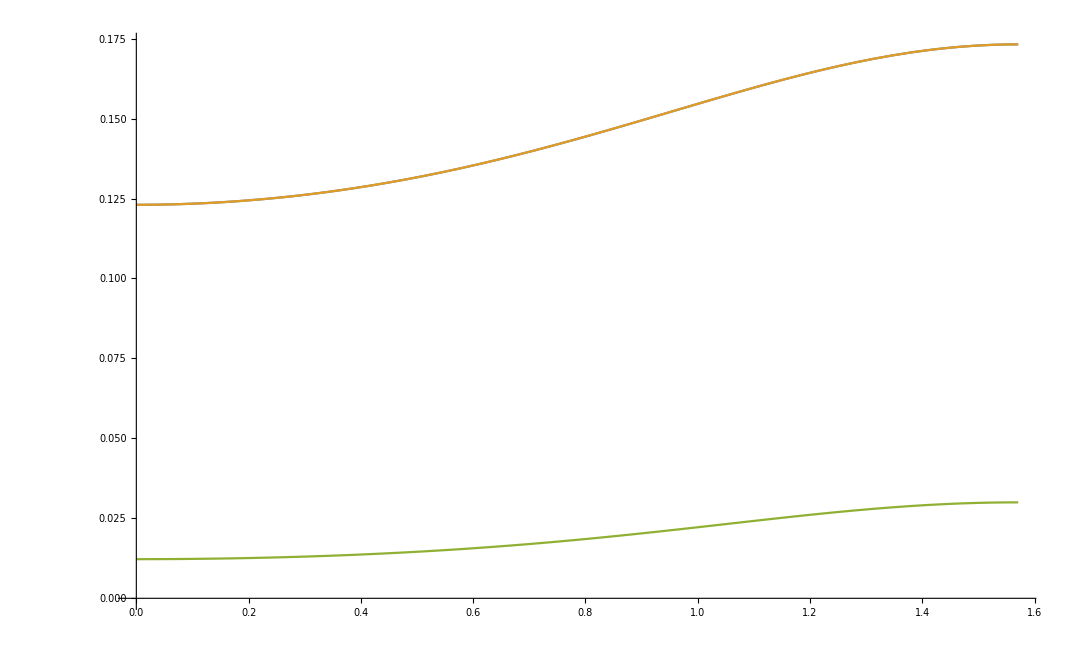

```mathematica
v=0.5;mD=0.15;
Plot[{Re[√Πpar[θ,v,mD]], Re[√Conjugate[Πpar[θ,v,mD]]],Re[Πpar[θ,v,mD]]},{θ,0,π/2}]
```

```mathematica
{{Re[ⅈ √Πpar[θ,v,mD]],Im[ⅈ √Πpar[θ,v,mD]]},{Re[-ⅈ √Πpar[θ,v,mD]],Im[-ⅈ √Πpar[θ,v,mD]]},{Re[ⅈ √Conjugate[Πpar[θ,v,mD]]],Im[ⅈ √Conjugate[Πpar[θ,v,mD]]]},{Re[-ⅈ √Conjugate[Πpar[θ,v,mD]]],Im[-ⅈ √Conjugate[Πpar[θ,v,mD]]]}}
```

{{0.0483963,0.143643},{-0.0483963,-0.143643},{-0.0483963,0.143643},{0.0483963,-0.143643}}

### Definitions

```mathematica
αcont=SetPrecision[{0.5137193759431391,0.0024666827878353577},500]; 
σcont=SetPrecision[{0.16955497884544793,0.0008581023195660334},500];
ccont={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
Πpar[θ_,v_,mD_]:=SetPrecision[mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]),200];
Πper[θ_,β_,v_,mD_]:=SetPrecision[mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]),100];
```

## Coulombic part

### Real

```mathematica
ReVcpar[r_,mD_,v_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,v,mD]] Exp[-√Re[Πpar[θ,v,mD]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20]-α mD;
```

```mathematica
ReVcparcheck[r_,mD_,v_,α_]:=-α/π NIntegrate[p^2 Sin[θ] Exp[ⅈ r p Cos[θ]]/(p^2+Re[Πpar[θ,v,mD]]),{p,0,∞},{θ,0,π}]-α mD;
```

```mathematica
Quiet[ParallelTable[ReVcparcheck[10^a,15/100,1/2,αcont[[1]]],{a,-10,10}]]
```

```mathematica
Table[{a,ReVcpar[10^a,15/100,1/2,αcont[[1]]]},{a,-10,10}]
```

{{-10,-5.13719×10^9},{-9,-5.13719×10^8},{-8,-5.13719×10^7},{-7,-5.13719×10^6},{-6,-513719.},{-5,-51371.9},{-4,-5137.19},{-3,-513.72},{-2,-51.3727},{-1,-5.13836},{0,-0.51913},{1,-0.0860798},{2,-0.0770174},{3,-0.0770579},{4,-0.0770579},{5,-0.0770579},{6,-0.0770579},{7,-0.0770579},{8,-0.0770579},{9,-0.0770579},{10,-0.0770579}}

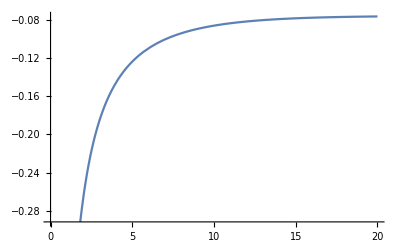

```mathematica
Plot[ReVcpar[r,0.15,0.5,αcont[[1]]],{r,0,20}]
```

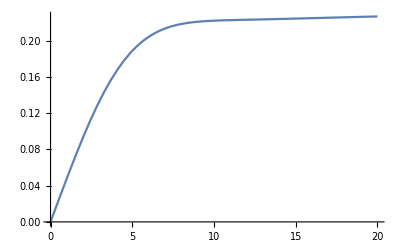

```mathematica
Plot[ReVsinter[r],{r,0,20}]
```

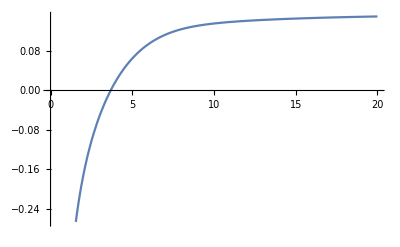

```mathematica
Plot[ReVcpar[r,0.15,0.5,αcont[[1]]]+ReVsinter[r],{r,0,20}]
```

### Imaginary

```mathematica
ImVcparcheck[r_,mD_,v_,α_,T_]:=-α T mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2 (1+v^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞},{θ,0,π}]
```

```mathematica
ImVcpar[r_,mD_,v_,α_,T_]:=α T mD^2(1-v^2)^(3/2)NIntegrate[Re[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]])],{θ,0,π/2},Method->"GlobalAdaptive",WorkingPrecision->11,AccuracyGoal->11];
```

```mathematica
Quiet[ParallelTable[{a,ImVcparcheck[10^a,15/100,1/2,αcont[[1]],155/1000]},{a,-10,10}]]
```

$Aborted

```mathematica
ParallelTable[{a,ImVcpar[10^a,15/100,1/2,αcont[[1]],155/1000]},{a,-10,10}]
```

{{-10,-0.037839746187},{-9,-0.037839746187},{-8,-0.037839746187},{-7,-0.037839746187},{-6,-0.037839746187},{-5,-0.037839746186},{-4,-0.037839746148},{-3,-0.037839743063},{-2,-0.037839508472},{-1,-0.03782344325},{0,-0.03695447438},{1,-0.016934290667},{2,-0.00012591221651},{3,-0.000017006509386},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

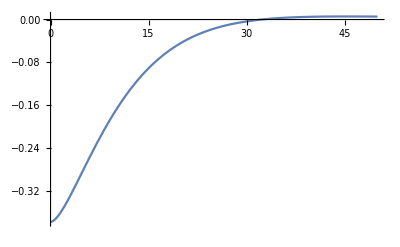

```mathematica
Plot[ImVcpar[r,15/100,1/2,αcont[[1]],155/100],{r,0,50}]
```

```mathematica
ImVc0[r_,mD_,α_,T_]:=-α T Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[mD r z],{z,0,∞}]];
```

```mathematica
Quiet[ParallelTable[{a,ImVc0[10^a,15/100,αcont[[1]],155/1000]},{a,-10,10}]]
```

{{-10,-0.0796265},{-9,-0.0796265},{-8,-0.0796265},{-7,-0.0796265},{-6,-0.0796265},{-5,-0.0796265},{-4,-0.0796265},{-3,-0.0796265},{-2,-0.0796261},{-1,-0.0795969},{0,-0.0780375},{1,-0.0429296},{2,-0.000721662},{3,-7.07917×10^-6},{4,-7.07792×10^-8},{5,-7.07791×10^-10},{6,-7.07791×10^-12},{7,-7.07791×10^-14},{8,-7.07791×10^-16},{9,-7.07791×10^-18},{10,-7.07791×10^-20}}

```mathematica
ParallelTable[{a,ImVcpar[10^a,15/100,1/1000000,αcont[[1]],155/1000]},{a,-10,10}]
```

{{-10,-0.079626503271},{-9,-0.079626503271},{-8,-0.079626503271},{-7,-0.079626503271},{-6,-0.079626503271},{-5,-0.07962650327},{-4,-0.079626503211},{-3,-0.079626498222},{-2,-0.079626090982},{-1,-0.079597139927},{0,-0.078037768395},{1,-0.042929635042},{2,-0.0042744908143},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

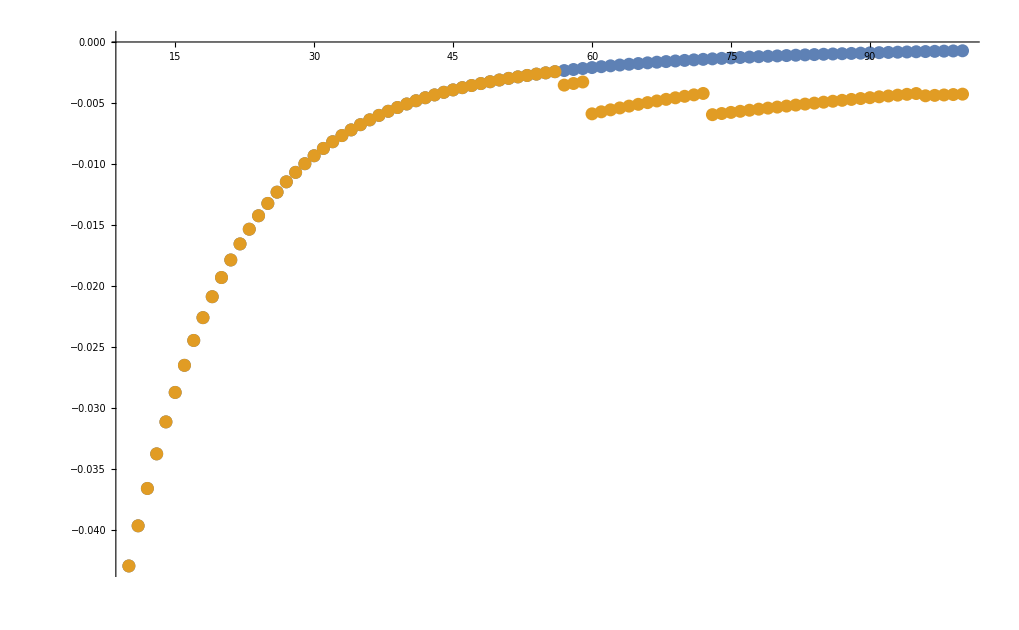

```mathematica
ListPlot[{Quiet[ParallelTable[{a,ImVc0[a,15/100,αcont[[1]],155/1000]},{a,10,100,1}]],Quiet[ParallelTable[{a,ImVcpar[a,15/100,1/1000000,αcont[[1]],155/1000]},{a,10,100,1}]]},PlotRange->All]
```

```mathematica
ImVcparcheck[10^2,15/100,1/1000000,αcont[[1]],155/100]
```

-0.00721662-1.21818×10^-15 ⅈ

```mathematica
ImVcparinter[r1_,mD1_,v1_,α1_,T1_]:=Block[{r=r1,mD=mD1,v=v1,α=α1,T=T1,tab,inter},tab=ParallelTable[SetPrecision[{θ,α T mD^2(1-v^2)^(3/2)Re[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]])]},100],{θ,0,π/2,10^-4}];
inter=Interpolation[tab];
Return[NIntegrate[inter[x],{x,0,π/2},AccuracyGoal->10]]];
```

```mathematica
Quiet[ParallelTable[{a,ImVc0[10^a,15/100,αcont[[1]],155/1000]},{a,-10,10}]]
```

{{-10,-0.0796265},{-9,-0.0796265},{-8,-0.0796265},{-7,-0.0796265},{-6,-0.0796265},{-5,-0.0796265},{-4,-0.0796265},{-3,-0.0796265},{-2,-0.0796261},{-1,-0.0795969},{0,-0.0780375},{1,-0.0429296},{2,-0.000721662},{3,-7.07917×10^-6},{4,-7.07792×10^-8},{5,-7.07791×10^-10},{6,-7.07791×10^-12},{7,-7.07791×10^-14},{8,-7.07791×10^-16},{9,-7.07791×10^-18},{10,-7.07791×10^-20}}

```mathematica
ImVcparinter[10^3,15/100,1/1000000,αcont[[1]],155/100]//AbsoluteTiming
```

{35.4695,-0.0000707955}

## String Part

### Real

```mathematica
gReAn[r_,mD_,v_,α_]:=2 α/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,v,mD]]Exp[-r Cos[θ] √Re[Πpar[θ,v,mD]]],{θ,0,π/2}]-α NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,v,mD]]^(3/2)Exp[-r Cos[θ] √Re[Πpar[θ,v,mD]]],{θ,0,π/2}]+mD^2 ReVcpar[r,mD,v,α];
```

```mathematica
gReAn[0.00000000000000000000000000000000001,0.0001,0.5,αcont[[1]]]
```

-7.50063×10^25

```mathematica
Quiet[ParallelTable[{a,gReAn[10^a,15/100,0,αcont[[1]]]},{a,-13,5}]]
```

{{-13,-0.00167847},{-12,-0.00172615},{-11,-0.00173306},{-10,-0.00173375},{-9,-0.0017338},{-8,-0.0017338},{-7,-0.0017338},{-6,-0.0017338},{-5,-0.0017338},{-4,-0.0017338},{-3,-0.0017338},{-2,-0.0017338},{-1,-0.0017338},{0,-0.0017338},{1,-0.0017338},{2,-0.0017338},{3,-0.0017338},{4,-0.0017338},{5,-0.0017338}}

```mathematica
Quiet[ParallelTable[{a,gReAn[-10^a,15/100,0,αcont[[1]]]},{a,-13,2}]]
```

{{-13,-0.00180054},{-12,-0.00174141},{-11,-0.00173426},{-10,-0.00173387},{-9,-0.00173381},{-8,-0.0017338},{-7,-0.0017338},{-6,-0.0017338},{-5,-0.0017338},{-4,-0.0017338},{-3,-0.0017338},{-2,-0.0017338},{-1,-0.0017338},{0,-0.0017338},{1,-0.0017338},{2,-0.0017338}}

```mathematica
gReAn[10^-30,15/100,0,αcont[[1]]]
```

6.59707×10^12

```mathematica
(*reduces to numerical version of delta function as requried*)
```

```mathematica
gReAntab=Join[ParallelTable[{r,Re[gReAn[r,15/100,1/2,αcont[[1]]]]},{r,10^-10,10^-5,10^-10}],ParallelTable[{r,Re[gReAn[r,15/100,1/2,αcont[[1]]]]},{r,2 10^-5,10^-1,10^-5}],ParallelTable[{r,Re[gReAn[r,15/100,1/2,αcont[[1]]]]},{r,2 10^-1,100,10^-1}],ParallelTable[{r,Re[gReAn[r,15/100,1/2,αcont[[1]]]]},{r,101,10^5,1}]];//AbsoluteTiming
```

{2500.03,Null}

```mathematica
gReAninter=Interpolation[gReAntab];
```

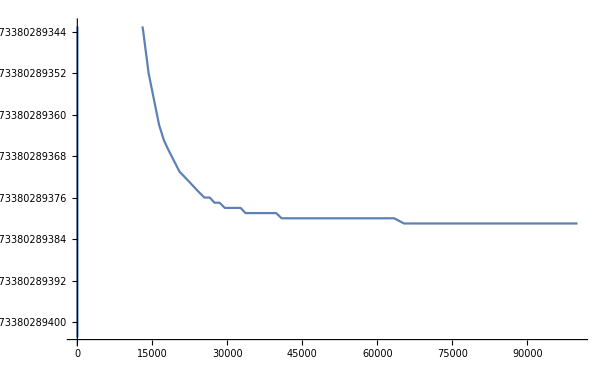

```mathematica
Plot[gReAninter[x],{x,10^-10,10^5}]
```

```mathematica
NIntegrate[gReAninter[s],{s,10^-10,10}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {9.72139×10^-10}. NIntegrate obtained -0.0565167 and 0.0000736034 for the integral and error estimates.

-0.0565167

```mathematica
D[ParabolicCylinderD[-1/2, √2 μ r],r]
```

√2 μ ((r μ ParabolicCylinderD[-1/2,√2 r μ])/(√2)-ParabolicCylinderD[1/2,√2 r μ])

```mathematica
W[x_,μ_]:=√2 μ ((x μ ParabolicCylinderD[-1/2,√2 x μ])/(√2)-ParabolicCylinderD[1/2,√2 x μ])Im[ParabolicCylinderD[-1/2,ⅈ √2 μ x]]-ParabolicCylinderD[-1/2,√2 μ x] √2 Re[μ ((ⅈ x μ ParabolicCylinderD[-1/2,ⅈ √2 x μ])/(√2)-ParabolicCylinderD[1/2,ⅈ √2 x μ])];
```

```mathematica
N[W[10^5,65]]
```

65.

```mathematica
ReVs[r_,mD_,α_,σ_]:=Im[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[(ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4) s] s^2 gReAninter[s])/((mD^2 σ/α)^(1/4)),{s,r,10^5},MaxRecursion->20,WorkingPrecision->10]]+ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[(Im[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) s]] s^2 gReAninter[s])/((mD^2 σ/α)^(1/4)),{s,0,r},MaxRecursion->20,WorkingPrecision->10]];
```

```mathematica
ReVs[100,10/10000,αcont[[1]],σcont[[1]]]
```

5120.457573

```mathematica
Limit[ParabolicCylinderD[-1/2,ⅈ a],a->0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
ReVstab=ParallelTable[{r,ReVs[r,15/100,αcont[[1]],σcont[[1]]]},{r,10^-10,100,1/10}];
```

```mathematica
ReVsinter=Interpolation[ReVstab];
```

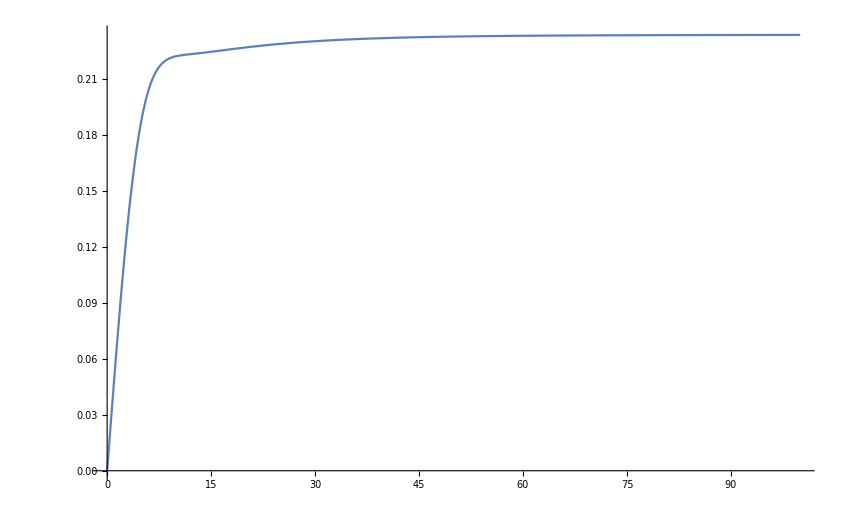

```mathematica
Plot[ReVsinter[x],{x,10^-10,100},PlotRange->All]
```

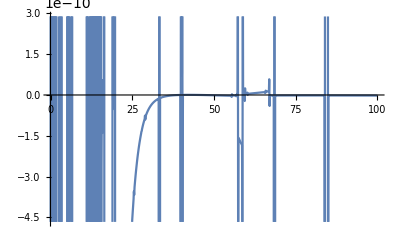

```mathematica
Plot[-1/x^2 ReVsinter''[x]+((15/100)^2 σcont[[1]]/αcont[[1]])ReVsinter[x]+gReAninter[x],{x,10^-2,100}]
```

```mathematica
ReVsold[r_,mD_,α_,σ_]:=Gamma[1/4]/(2^(3/4)√π)σ/((mD^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]+Gamma[1/4]/(2 Gamma[3/4])σ/((mD^2 σ/α)^(1/4));
```

### Imaginary

```mathematica
-D[Sinh[r Cos[θ] √f[θ,v,mD]]SinhIntegral[r Cos[θ] √f[θ,v,mD]]-Cosh[r Cos[θ] √f[θ,v,mD]]CoshIntegral[r Cos[θ] √f[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[f[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[f[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]],{r,2}]-2/r D[Sinh[r Cos[θ] √f[θ,v,mD]]SinhIntegral[r Cos[θ] √f[θ,v,mD]]-Cosh[r Cos[θ] √f[θ,v,mD]]CoshIntegral[r Cos[θ] √f[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[f[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[f[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]],r]//FullSimplify
```

1/r Cos[θ] (2 √Conjugate[f[θ,v,mD]] (-CoshIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]] Sinh[r √Conjugate[f[θ,v,mD]] Cos[θ]]+Cosh[r √Conjugate[f[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]])+r Conjugate[f[θ,v,mD]] Cos[θ] (-Cosh[r √Conjugate[f[θ,v,mD]] Cos[θ]] CoshIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]]+Sinh[r √Conjugate[f[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]])+√f[θ,v,mD] (CoshIntegral[r Cos[θ] √f[θ,v,mD]] (r Cos[θ] Cosh[r Cos[θ] √f[θ,v,mD]] √f[θ,v,mD]+2 Sinh[r Cos[θ] √f[θ,v,mD]])-(2 Cosh[r Cos[θ] √f[θ,v,mD]]+r Cos[θ] √f[θ,v,mD] Sinh[r Cos[θ] √f[θ,v,mD]]) SinhIntegral[r Cos[θ] √f[θ,v,mD]]))

```mathematica
gImAninter[r1_,mD1_,v1_,α1_,T1_]:=Block[{r=r1,mD=mD1,v=v1,α=α1,T=T1,inter,tab},tab=SetPrecision[ParallelTable[{θ,Re[Cos[θ] Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(2 √Conjugate[Πpar[θ,v,mD]] (-CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+r Conjugate[Πpar[θ,v,mD]] Cos[θ] (-Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+√Πpar[θ,v,mD] (CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]] (r Cos[θ] Cosh[r Cos[θ] √Πpar[θ,v,mD]] √Πpar[θ,v,mD]+2 Sinh[r Cos[θ] √Πpar[θ,v,mD]])-(2 Cosh[r Cos[θ] √Πpar[θ,v,mD]]+r Cos[θ] √Πpar[θ,v,mD] Sinh[r Cos[θ] √Πpar[θ,v,mD]]) SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]))]},{θ,0,π/2,1/10000}],100];
inter=Interpolation[tab];
Return[α T mD^2(1-v^2)^(3/2)1/r NIntegrate[inter[x],{x,0,π/2}]+mD^2 ImVcpar[r,mD,v,α,T]]];
```

```mathematica
gImAn[r_,mD_,v_,α_,T_]:=α T mD^2(1-v^2)^(3/2)1/r NIntegrate[Re[Cos[θ] Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(2 √Conjugate[Πpar[θ,v,mD]] (-CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+r Conjugate[Πpar[θ,v,mD]] Cos[θ] (-Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+√Πpar[θ,v,mD] (CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]] (r Cos[θ] Cosh[r Cos[θ] √Πpar[θ,v,mD]] √Πpar[θ,v,mD]+2 Sinh[r Cos[θ] √Πpar[θ,v,mD]])-(2 Cosh[r Cos[θ] √Πpar[θ,v,mD]]+r Cos[θ] √Πpar[θ,v,mD] Sinh[r Cos[θ] √Πpar[θ,v,mD]]) SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]))],{θ,0,π/2},Method->"GlobalAdaptive",WorkingPrecision->25,AccuracyGoal->10,MaxRecursion->20]+mD^2 ImVcpar[r,mD,v,α,T];
```

```mathematica
gold[r_,mD_,α_,T_]:=-α T mD^2 Quiet[2NIntegrate[p/(p^2+1)Sinc[p mD r],{p,0,∞}]];
```

```mathematica
Quiet[ParallelTable[{a,gold[10^a,15/100,αcont[[1]],155/1000]},{a,-10,10}]]
```

{{-10,-0.0903437},{-9,-0.0825681},{-8,-0.0743184},{-7,-0.0660669},{-6,-0.0580515},{-5,-0.0495657},{-4,-0.0413151},{-3,-0.0330645},{-2,-0.0248393},{-1,-0.016564},{0,-0.00835509},{1,-0.00141521},{2,-0.0000158834},{3,-1.59267×10^-7},{4,-1.59253×10^-9},{5,-1.59253×10^-11},{6,-1.59253×10^-13},{7,-1.59253×10^-15},{8,-1.59253×10^-17},{9,-1.59253×10^-19},{10,-1.59253×10^-21}}

```mathematica
ParallelTable[{a,gImAn[10^a,15/100,1/1000000,αcont[[1]],155/1000]},{a,-10,10}]
```

{{-10,-0.0908187224911},{-9,-0.0825681178722},{-8,-0.0743175118974},{-7,-0.0660669059227},{-6,-0.0578162999479},{-5,-0.0495656939751},{-4,-0.0413150880025},{-3,-0.0330644821759},{-2,-0.0248138869526},{-1,-0.016564008437},{0,-0.0083550949859},{1,-0.0014152094313},{2,-0.00009601449501},{3,7.471162999851747590635598×10^-11},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

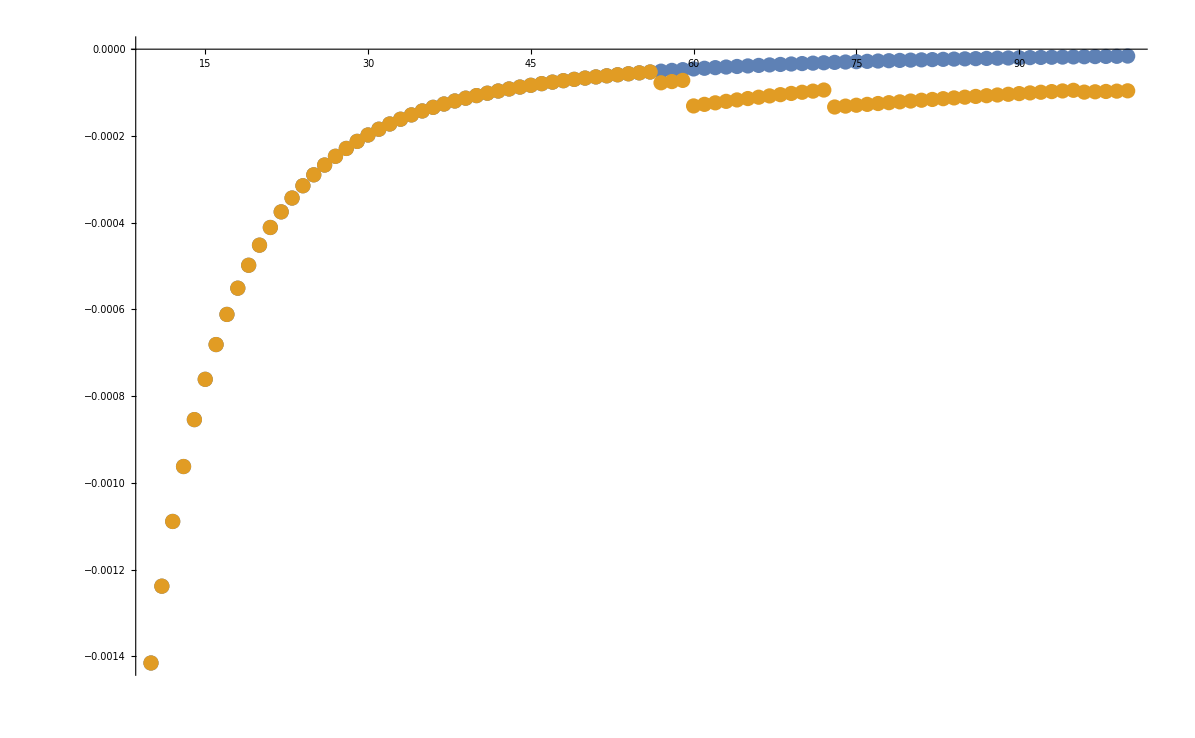

```mathematica
ListPlot[{Quiet[ParallelTable[{a,gold[a,15/100,αcont[[1]],155/1000]},{a,10,100,1}]],Quiet[ParallelTable[{a,gImAn[a,15/100,1/1000000,αcont[[1]],155/1000]},{a,10,100,1}]]},PlotRange->All]
```

```mathematica
gImAntab=Join[ParallelTable[{r,Re[gImAn[r,15/100,1/2,αcont[[1]],155/1000]]},{r,10^-10,10^-5,10^-10}],ParallelTable[{r,Re[gImAn[r,15/100,1/2,αcont[[1]],155/1000]]},{r,2 10^-5,10^-1,10^-5}],ParallelTable[{r,Re[gImAn[r,15/100,1/2,αcont[[1]],155/1000]]},{r,2 10^-1,100,10^-1}],ParallelTable[{r,Re[gImAn[r,15/100,,1/2,αcont[[1]],155/1000]]},{r,101,10^3,1}]];//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$665835`θ near {Notebook$$16$665835`θ} = {1.570796326794896619231321691627966895941026249884264811939709}. NIntegrate obtained -1267.088942252651192892481877013297209509875679610726119183509 and 225.47066834089994205898628680884064577384082191167590337462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$665835`θ near {Notebook$$16$665835`θ} = {1.570796326794896619231321691627966895941026249884264811939709}. NIntegrate obtained -1267.094292105356282022866610534193466138300511410276722909665 and 225.4706683128590838737162245051805969301131599565878131397675 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$665835`θ near {Notebook$$16$665835`θ} = {1.570796326794896619231321691627966895941026249884264811939709}. NIntegrate obtained -1267.094224373022477145651998677467482678677190554400429204963 and 225.4706683120153526123966981421291137019764124031588217372567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$665835`θ near {Notebook$$16$665835`θ} = {1.570796326794896619231321691627966895941026249884264811939709}. NIntegrate obtained -1267.094157278610587332856345703253299938765536645626329498402 and 225.4706683111729509826928952547684607829830672304261168611253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1061.05,Null}

```mathematica
gImAninter=Interpolation[gImAntab];
```

```mathematica
ImVspar[r_,mD_,v_,α_,σ_,T_]:=ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4)s]] s^2 gImAninter[s],{s,0,r}]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4)r]]NIntegrate[ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)s] s^2 gImAninter[s],{s,r,10^3}]-ParabolicCylinderD[-1/2,0]NIntegrate[ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)s] s^2 gImAninter[s],{s,0,10^3}];
```

```mathematica
Quiet[ImVspar[10,15/100,1/2,αcont[[1]],σcont[[1]],155/1000]]
```

NIntegrate::inumr: The integrand s^2 «1» InterpolatingFunction[{{1.×10^-10,1000.}},{5,3,0,{111898},{4},0,0,0,0,Automatic,{},{},False},{{1/10000000000,«49»,«111848»}},{{-0.0493427266733429},{-0.0479937247184922},{-0.0472046091615051},{-0.0466447227636416},{-0.0462104411343172},{-0.0458556072066545},{-0.0455555993955276},{-0.045295720808791},«35»,{-0.0419779427474278},{-0.0419342061106417},{-0.0418914307968834},{-0.0418495754540382},{-0.0418086013421026},{-0.0417684721177124},{-0.041729153640441},«111848»},{Automatic}][s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{500.,1000}}.

NIntegrate::inumr: The integrand s^2 «1» InterpolatingFunction[{{1.×10^-10,1000.}},{5,3,0,{111898},{4},0,0,0,0,Automatic,{},{},False},{{1/10000000000,«49»,«111848»}},{{-0.0493427266733429},{-0.0479937247184922},{-0.0472046091615051},{-0.0466447227636416},{-0.0462104411343172},{-0.0458556072066545},{-0.0455555993955276},{-0.045295720808791},«35»,{-0.0419779427474278},{-0.0419342061106417},{-0.0418914307968834},{-0.0418495754540382},{-0.0418086013421026},{-0.0417684721177124},{-0.041729153640441},«111848»},{Automatic}][s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{505.,1000}}.

-0.014876-1/(2^(1/4) Gamma[3/4])√π NIntegrate[ParabolicCylinderD[-1/2,√2 (((3/20)^2 0.1695549788454479289701026800685212947428226470947265625)/0.5137193759431391004710576453362591564655303955078125)^(1/4) s] s^2 gImAninter[s],{s,0,10^3}]+26.4680369480394885913103534197041563998175466615537219592723333152974015596600601084210882709055359447492546450377256616190657111372350740705316136661861444774863424873038069176722959761933744558557344431127315801961425296000283127180106447096977888388407773888706833510722913023840048861397820306691511987670043283849356656832542849625708590730516468353076359220084981678198037052957454425645216464519071392348035492743085569397519864511101622105659616189794275467477470967327613201150411349487207 NIntegrate[ParabolicCylinderD[-1/2,√2 (((3/20)^2 0.1695549788454479289701026800685212947428226470947265625)/0.5137193759431391004710576453362591564655303955078125)^(1/4) s] s^2 gImAninter[s],{s,10,10^3}]